```mathematica
(* Load QMB *)
Get[StringJoin[DirectoryName[NotebookDirectory[]],"Kernel/init.m"]]
```

## BoseHubbardHamiltonian

Hamiltoniano para 3 bosones y 3 sitios con J=U=1 con condiciones de frontera abiertas:

```mathematica
n=L=3;
J=U=1.;
BoseHubbardHamiltonian[n,L,J,U]//MatrixForm
```

(3. | -1.73205 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.73205 | 1. | -1. | -2. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 1. | 0. | -1.41421 | 0. | 0. | 0. | 0. | 0.
0. | -2. | 0. | 1. | -1.41421 | 0. | -1.73205 | 0. | 0. | 0.
0. | 0. | -1.41421 | -1.41421 | 0. | -1.41421 | 0. | -1.41421 | 0. | 0.
0. | 0. | 0. | 0. | -1.41421 | 1. | 0. | 0. | -1. | 0.
0. | 0. | 0. | -1.73205 | 0. | 0. | 3. | -1.73205 | 0. | 0.
0. | 0. | 0. | 0. | -1.41421 | 0. | -1.73205 | 1. | -2. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 0. | -2. | 1. | -1.73205
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.73205 | 3.)

Mismo Hamiltoniano, pero en los sectores de simetría de paridad par e impar:

```mathematica
MatrixForm/@{BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"],BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"OddParity"]}
```

{(3. | -1.73205 | 0. | 0. | 0. | 0.
-1.73205 | 1. | -1. | -2. | 0. | 0.
0. | -1. | 1. | 0. | -2. | 0.
0. | -2. | 0. | 1. | -2. | -2.44949
0. | 0. | -2. | -2. | 0. | 0.
0. | 0. | 0. | -2.44949 | 0. | 3.),(3. | -1.73205 | 0. | 0.
-1.73205 | 1. | -1. | -2.
0. | -1. | 1. | 0.
0. | -2. | 0. | 1.)}

Definición de la rutina:

```mathematica
?BoseHubbardHamiltonian
```

## PeriodicBoseHubbard

Generate the Hamiltonian for n=3 sites, m=3 bosons and J=U=1:

```mathematica
Module[{n=3,m=3,J=1,U=1,BH},
BH=PeriodicBoseHubbard[n,m,J,U];
BH//MatrixForm]
```

(3 | -1.73205 | 0 | 0 | -1.73205 | 0 | 0 | 0 | 0 | 0
-1.73205 | 1 | -2. | 0 | -1. | -1.41421 | 0 | 0 | 0 | 0
0 | -2. | 1 | -1.73205 | 0 | -1.41421 | -1. | 0 | 0 | 0
0 | 0 | -1.73205 | 3 | 0 | 0 | -1.73205 | 0 | 0 | 0
-1.73205 | -1. | 0 | 0 | 1 | -1.41421 | 0 | -2. | 0 | 0
0 | -1.41421 | -1.41421 | 0 | -1.41421 | 0 | -1.41421 | -1.41421 | -1.41421 | 0
0 | 0 | -1. | -1.73205 | 0 | -1.41421 | 1 | 0 | -2. | 0
0 | 0 | 0 | 0 | -2. | -1.41421 | 0 | 1 | -1. | -1.73205
0 | 0 | 0 | 0 | 0 | -1.41421 | -2. | -1. | 1 | -1.73205
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.73205 | -1.73205 | 3)

## MomentumSectorPeriodicBoseHubbard

You can use the full sectorized hamiltonian

```mathematica
Module[{n=3,m=3,J=1,U=1,BH},
BH=MomentumSectorPeriodicBoseHubbard[n,m,J,U,All];
BH//MatrixForm]
```

(3. | -1.73205 | -1.73205 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.73205 | 1. | -3. | -2.44949 | 0 | 0 | 0 | 0 | 0 | 0
-1.73205 | -3. | 1. | -2.44949 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2.44949 | -2.44949 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3. | -1.73205 | -1.73205 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.73205 | 1. | 0.+1.73205 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.73205 | 0.-1.73205 ⅈ | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3. | -1.73205 | -1.73205
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.73205 | 1. | 0.-1.73205 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.73205 | 0.+1.73205 ⅈ | 1.)

Or you can use a single momentum symmetry sector by changing the last option to a integer smaller or equal to max(N,L)

```mathematica
Module[{n=3,m=3,J=1,U=1,BH},
BH=MomentumSectorPeriodicBoseHubbard[n,m,J,U,1];
BH//MatrixForm]
```

(3. | -1.73205 | -1.73205 | 0
-1.73205 | 1. | -3. | -2.44949
-1.73205 | -3. | 1. | -2.44949
0 | -2.44949 | -2.44949 | 0)

```mathematica
Module[{n=3,m=3,J=1,U=1,BH},
BH=MomentumSectorPeriodicBoseHubbard[n,m,J,U,2];
BH//MatrixForm]
```

(3. | -1.73205 | -1.73205
-1.73205 | 1. | 0.+1.73205 ⅈ
-1.73205 | 0.-1.73205 ⅈ | 1.)

# Neat examples

### NN spacing statistics

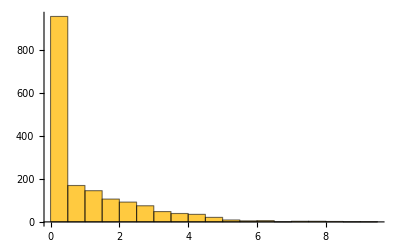

```mathematica
Module[{BH=PeriodicBoseHubbard[7,7,2,1],data},
data=Differences[Unfold[BH//Normal//Eigenvalues//Sort]["UnfoldedLevels"],1];
Histogram[data]]
```

### SFF calculation

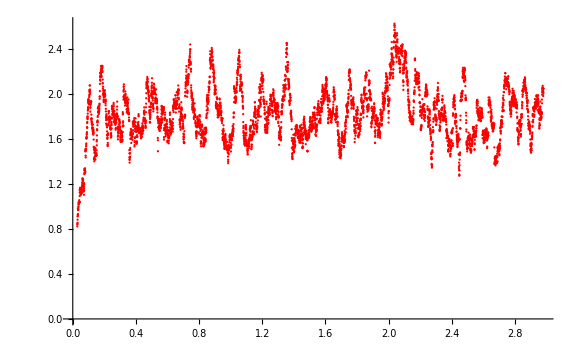

```mathematica
Module[{tH=2Pi,f=1/100,rate=20,tmax=3,bin=75,hamiltonian=PeriodicBoseHubbard[7,7,2,1],times,SFFDat,SmoothSFFDat},times=Range[f,tmax,f/rate];
SFFDat=With[{data=Unfold[hamiltonian//Normal//Eigenvalues//Sort]["UnfoldedLevels"]},{#,SpectralFormFactor[data,tH #]}&/@times];
bin=75;
SmoothSFFDat=With[{tim=MovingAverage[First/@SFFDat,bin],dat=MovingAverage[Last/@SFFDat,bin]},{tim[[#]],dat[[#]]}&/@Range[tim//Length]];
Show[{ListPlot[SmoothSFFDat,PlotStyle->{Red},ImageSize->Large,AxesLabel->{" ", ""},AxesStyle->Directive[Black, 22]]}]]
```

```mathematica
tH=2 Pi;f=1/100;rate=20.;tmax=3;
times=Range[f,tmax,f/rate];
SFFDat=With[{data=Unfold[UnitaryData]["UnfoldedLevels"]},{#,SFF[data,tH #]}&/@times];
bin=75;
SmoothSFFDat=With[{tim=MovingAverage[First/@SFFDat,bin],dat=MovingAverage[Last/@SFFDat,bin]},{tim[[#]],dat[[#]]}&/@Range[tim//Length]];
```

```mathematica
GOESFF[t_]:=If[t<1,2t-t*Log[1+2*t],2-t*Log[(2t+1)/(2t-1)]];
```